```mathematica
Clear["Global`*"]
```

Create n/n_0 curves for fixed ΔΦ, variable R_B

## Distribution funcs

```mathematica
vbthK[dPhi_,Tm_,kappa_]:=√(dPhi/(Tm(1-3/(2 kappa))));
vbth[dPhi_,Tm_]:=√(dPhi/Tm);
```

### Dist. funcs in Cartesian

```mathematica
MaxwellianArbPot[vpar_,vperp_,vbth_,alpha_]:=1/π^(3/2)Exp[-(vperp^2+vpar^2-2 vbth(vpar^2+(1-alpha)vperp^2-vbth^2)^(1/2))]UnitStep[vpar]
```

```mathematica
KappaArbPot[vpar_,vperp_,vbth_,alpha_,kappa_]:=2/(√π(1-3/(2kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(vperp^2+vpar^2-2 vbth(vpar^2+(1-alpha)vperp^2-vbth^2)^(1/2))/(kappa-3/2))^(-(kappa+1))
```

```mathematica
MaxwellianArbPotUnitStep[vpar_,vperp_,vbth_,alpha_]:=1/π^(3/2)Exp[-(vperp^2+vpar^2-2 vbth(vpar^2+(1-alpha)vperp^2-vbth^2)^(1/2))]UnitStep[vpar^2+(1-alpha)vperp^2-vbth^2]
```

```mathematica
KappaArbPotUnitStep[vpar_,vperp_,vbth_,alpha_,kappa_]:=2/(√π(1-3/(2kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(vperp^2+vpar^2-2 vbth(vpar^2+(1-alpha)vperp^2-vbth^2)^(1/2))/(kappa-3/2))^(-(kappa+1))UnitStep[vpar^2+(1-alpha)vperp^2-vbth^2]
```

### Dist. functions in cylindrical coordinates

```mathematica
MaxwellArbPotCyl[rho_,phi_,vbth_,alpha_]:=2/(√π)Exp[-(rho^2-2 vbth(rho^2(1-alpha (Sin[phi])^2)-vbth^2)^(1/2))];
MaxwellArbPotCylUnitStep[rho_,phi_,vbth_,alpha_]:=2/(√π)Exp[-(rho^2-2 vbth(rho^2(1-alpha (Sin[phi])^2)-vbth^2)^(1/2))]UnitStep[rho^2(1-alpha(Sin[phi])^2)-vbth^2];
```

```mathematica
KappaArbPotCyl[rho_,phi_,vbth_,alpha_,kappa_]:=2/(√π(1-3/(2kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(rho^2-2 vbth(rho^2(1-alpha (Sin[phi])^2)-vbth^2)^(1/2))/(kappa-3/2))^(-(kappa+1))
```

```mathematica
KappaArbPotCylUnitStep[rho_,phi_,vbth_,alpha_,kappa_]:=2/(√π(1-3/(2kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(rho^2-2 vbth(rho^2(1-alpha (Sin[phi])^2)-vbth^2)^(1/2))/(kappa-3/2))^(-(kappa+1))UnitStep[rho^2(1-alpha(Sin[phi])^2)-vbth^2];
```

## Visualize

```mathematica
dPhi=941;Tm=110;
```

#### Parametric Maxwellian

```mathematica
Manipulate[ParametricPlot3D[{rho Cos[phi],rho Sin[phi],MaxwellArbPotCylUnitStep[rho,phi,vbth[dPhi,Tm],alpha]},{rho,0,6},{phi,-π/2,π/2},PlotRange->All,PlotPoints->20,ImageSize->800],{{alpha,1},0.001,1}]
```

```mathematica
Manipulate[ContourPlot[MaxwellianArbPot[vpar,vperp,vbth[dPhi,Tm],alpha],{vpar,0,8},{vperp,-4,4},ImageSize->600,PlotRange->Full],{{alpha,1},1,0.001}]
```

#### Parametric kappa

```mathematica
Manipulate[ContourPlot[KappaArbPot[vpar,vperp,vbth[dPhi,Tm],alpha,kappa],{vpar,0,8},{vperp,-4,4},ImageSize->600,PlotRange->Full,ColorFunction->GrayLevel],{{alpha,1},1,0.001},{{kappa,3},1.5,10}]
```

## Generate curves

```mathematica
dPhi=941;Tm=110;
```

```mathematica
minRhoInteg=0;maxRhoInteg=12;
```

```mathematica
alphaList={1,1/2,1/3,1/4,1/5,1/7,1/8,1/10,1/15,1/18,1/20,1/25,1/30,1/40,1/50,1/60,1/70,1/80,1/90,1/100,1/130,1/170,1/200,1/250,1/300,1/400,1/500,1/600,1/700,1/800,1/1000,1/1500,1/2000,1/3000};
```

```mathematica
RBList=1/alphaList
```

{1,2,3,4,5,7,8,10,15,18,20,25,30,40,50,60,70,80,90,100,130,170,200,250,300,400,500,600,700,800,1000,1500,2000,3000}

```mathematica
MaxwellIntegList = (NIntegrate[rho^2 Sin[phi] MaxwellArbPotCylUnitStep[rho,phi,vbth[dPhi,Tm],#],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2}])&/@ alphaList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.69143,1.4275,2.23079,3.12638,4.09433,6.06769,7.00736,8.72201,12.0378,13.4996,14.3138,15.9373,17.1444,18.8104,19.9017,20.6703,21.2406,21.6802,22.0294,22.3135,22.917,23.4034,23.6449,23.9236,24.1087,24.3444,24.4872,24.5828,24.6515,24.703,24.7774,24.8724,24.9211,24.9698}

```mathematica
kappaEq1p6=(NIntegrate[rho^2 Sin[phi] KappaArbPotCylUnitStep[rho,phi,vbth[dPhi,Tm],#,16/10],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2}])&/@alphaList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
kappaEq1p8=(NIntegrate[rho^2 Sin[phi] KappaArbPotCylUnitStep[rho,phi,vbth[dPhi,Tm],#,18/10],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2}])&/@alphaList
```

```mathematica
kappaEq2=(NIntegrate[rho^2 Sin[phi] KappaArbPotCylUnitStep[rho,phi,vbth[dPhi,Tm],#,2],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2}])&/@alphaList
```

```mathematica
kappaEq3=(NIntegrate[rho^2 Sin[phi] KappaArbPotCylUnitStep[rho,phi,vbth[dPhi,Tm],#,3],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2}])&/@alphaList
```

```mathematica
MaxwellPlotList=Partition[Riffle[RBList,MaxwellIntegList],2]
```

{{1,0.69143},{2,1.4275},{3,2.23079},{4,3.12638},{5,4.09433},{7,6.06769},{8,7.00736},{10,8.72201},{15,12.0378},{18,13.4996},{20,14.3138},{25,15.9373},{30,17.1444},{40,18.8104},{50,19.9017},{60,20.6703},{70,21.2406},{80,21.6802},{90,22.0294},{100,22.3135},{130,22.917},{170,23.4034},{200,23.6449},{250,23.9236},{300,24.1087},{400,24.3444},{500,24.4872},{600,24.5828},{700,24.6515},{800,24.703},{1000,24.7774},{1500,24.8724},{2000,24.9211},{3000,24.9698}}

```mathematica
kappaEq1p6PlotList=Partition[Riffle[RBList,kappaEq1p6],2]
```

{{1,0.499742},{2,1.43038},{3,2.12701},{4,2.96125},{5,3.71271},{7,5.23944},{8,6.00119},{10,7.52512},{15,11.3429},{18,13.6397},{20,15.1733},{25,19.0152},{30,22.8661},{40,30.5847},{50,38.3069},{60,46.0099},{70,53.6713},{80,61.2709},{90,68.7906},{100,76.2154},{130,97.8105},{170,124.803},{200,143.644},{250,172.486},{300,198.397},{400,242.762},{500,279.132},{600,309.362},{700,334.826},{800,356.539},{1000,391.545},{1500,448.971},{2000,483.657},{3000,523.434}}

```mathematica
kappaEq1p8PlotList=Partition[Riffle[RBList,kappaEq1p8],2]
```

{{1,0.499736},{2,1.43117},{3,2.1295},{4,3.01862},{5,3.7866},{7,5.36858},{8,6.1547},{10,7.72344},{15,11.6337},{18,13.9721},{20,15.527},{25,19.397},{30,23.2364},{40,30.794},{50,38.1457},{60,45.2473},{70,52.0661},{80,58.5809},{90,64.7813},{100,70.6658},{130,86.5019},{170,103.912},{200,114.744},{250,129.609},{300,141.5},{400,159.303},{500,171.966},{600,181.421},{700,188.744},{800,194.581},{1000,203.295},{1500,216.014},{2000,222.9},{3000,230.173}}

```mathematica
kappaEq2PlotList=Partition[Riffle[RBList,kappaEq2],2]
```

{{1,0.499827},{2,1.42802},{3,2.1319},{4,3.03522},{5,3.80701},{7,5.40784},{8,6.20115},{10,7.78063},{15,11.6979},{18,14.0265},{20,15.5686},{25,19.3835},{30,23.1329},{40,30.3993},{50,37.3079},{60,43.8187},{70,49.9109},{80,55.5808},{90,60.838},{100,65.7012},{130,78.1885},{170,90.9635},{200,98.4573},{250,108.241},{300,115.695},{400,126.307},{500,133.494},{600,138.679},{700,142.595},{800,145.656},{1000,150.132},{1500,156.47},{2000,159.81},{3000,163.272}}

```mathematica
kappaEq3PlotList=Partition[Riffle[RBList,kappaEq3],2]
```

{{1,0.499989},{2,1.41613},{3,2.13423},{4,3.04558},{5,3.81757},{7,5.43777},{8,6.23566},{10,7.81395},{15,11.67},{18,13.9216},{20,15.3954},{25,18.9793},{30,22.4119},{40,28.7975},{50,34.5283},{60,39.6179},{70,44.1051},{80,48.0444},{90,51.4966},{100,54.5231},{130,61.6001},{170,67.9151},{200,71.2524},{250,75.2749},{300,78.1264},{400,81.9189},{500,84.3308},{600,86.0001},{700,87.2237},{800,88.1591},{1000,89.4947},{1500,91.3244},{2000,92.2609},{3000,93.2121}}

### Plots of ze results

```mathematica
nDigitsdPhi=3;nDigitsTm=3;
```

#### Full range

```mathematica
legendStyles=(Style[#,18])&/@{"κ = 1.6","κ = 1.8","κ = 2","κ = 3","Maxwellian"}
```

{κ = 1.6,κ = 1.8,κ = 2,κ = 3,Maxwellian}

ListLogLinearPlot::iodeg: 3 is not a valid interpolation order specification, or the given order is too high for the input array {None,None}.

General::stop: Further output of ListLogLinearPlot::iodeg will be suppressed during this calculation.

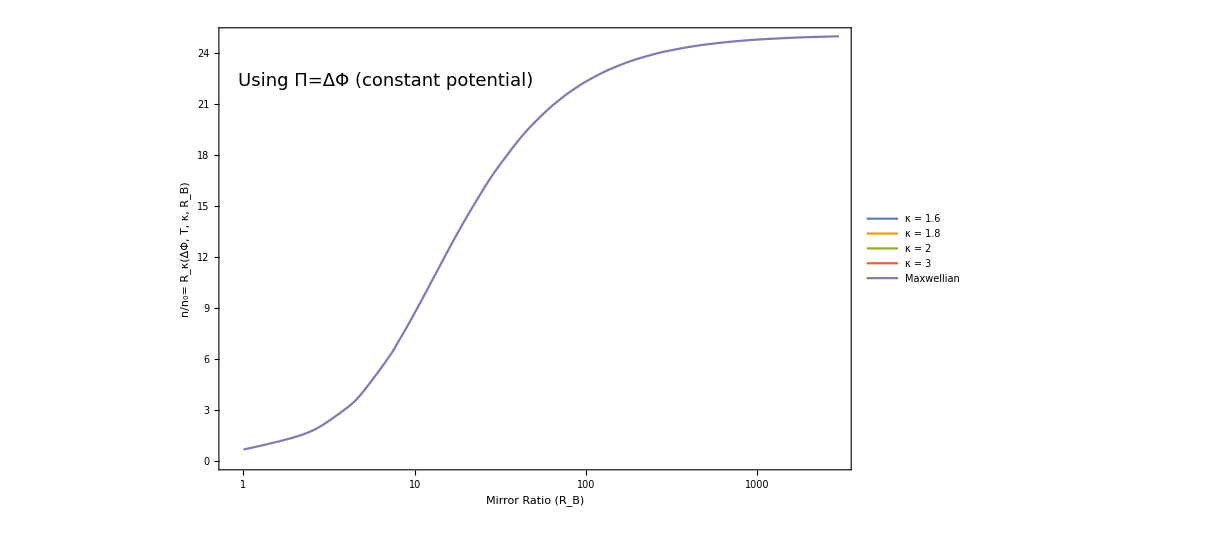

```mathematica
ListLogLinearPlot[{kappaEq1p6PlotList,kappaEq1p8PlotList,kappaEq2PlotList,kappaEq3PlotList,MaxwellPlotList},Joined->True,InterpolationOrder->3,PlotLegends->legendStyles,Frame->True,FrameStyle->Directive[Black,(FontSize->19)],PlotStyle->Directive[(FontSize->19)],FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio (R_B)"],StringForm["ΔΦ = `1` V; T_m = `2` eV; ϕ̄ = `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[Tm,nDigitsTm],NumberForm[N[dPhi/Tm],{3,1}]]}},Epilog->{Text[Style["Using Π=ΔΦ (constant potential)",18],Scaled[{0.03,0.9}],{-1,1}]},ImageSize->900]
```

#### Adjusted range

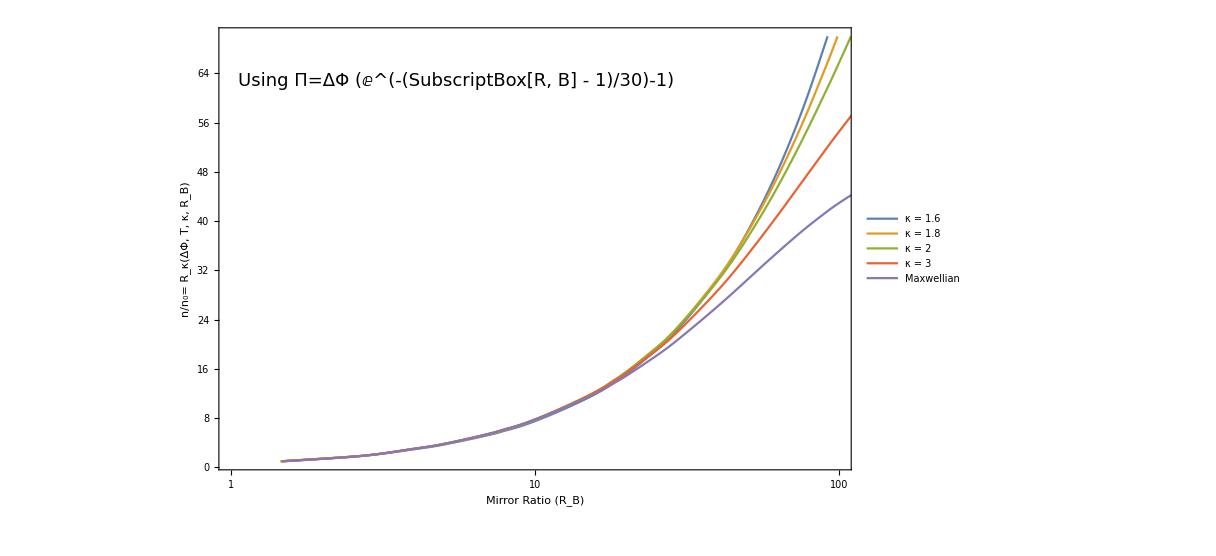

```mathematica
ListLogLinearPlot[{kappaEq1p6PlotList,kappaEq1p8PlotList,kappaEq2PlotList,kappaEq3PlotList,MaxwellPlotList},PlotRange->{{1,100},{1,70}},Joined->True,InterpolationOrder->3,PlotLegends->legendStyles,Frame->True,FrameStyle->Directive[Black,(FontSize->19)],PlotStyle->Directive[(FontSize->19)],FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio (R_B)"],StringForm["ΔΦ = `1` V; T_m = `2` eV; ϕ̄ = `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[Tm,nDigitsTm],NumberForm[N[dPhi/Tm],{3,1}]]}},Epilog->{Text[Style["Using Π=ΔΦ (constant potential)",18],Scaled[{0.03,0.9}],{-1,1}]},ImageSize->900]
```